```mathematica
ClearAll["Global`*"]
```

## Exact solution

```mathematica
intanalytic[n_,p_, β_]:=BesselI[n+p,β];
matanalytic[p_,β_,N0_]:=Table[intanalytic[i-j,p,2N0*β],{i,1,N0},{j,1,N0}];
partitionfunc[β_,N0_]:=Sum[Det[matanalytic[p,β,N0]],{p,-35,35}];
w1analytic[λ_,N0_]:=(D[partitionfunc[β,N0],β]/partitionfunc[β,N0]/(2N0^2))/.β->N[1/λ];
partitionfuncuN[β_,N0_]:=Det[matanalytic[0,β,N0]];
w1analyticuN[λ_,N0_]:=(D[partitionfuncuN[β,N0],β]/partitionfuncuN[β,N0]/(2N0^2))/.β->N[1/λ];
w1analyticthooft[λ_]/;0<=λ<=2:=1-λ/4;
w1analyticthooft[λ_]/;λ>2:=1/λ;
```

## Some function

```mathematica
lastsort = #~Extract~Ordering[#, -1] &;
canonize[w[m_,n_]]:=w@@(lastsort[{{m,n},{n,m},{-m,-n},{-n,-m}}]);
canonize[1]=1;
canonize[w[m_]]:=w@@(lastsort[{{m},{-m}}]);
```

## SU(3)

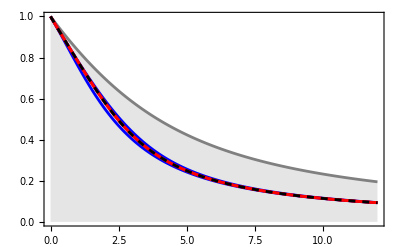

```mathematica
N0=3;
w[i_,j_,k_]:=-2/N0^2canonize@ w[i+j+k,0]+1/N0 canonize@w[i,j+k]+1/N0 canonize@w[j,i+k]+1/N0 canonize@w[k,j+i]+1/N0 canonize@w[j-i,k-i]-1/N0^2 canonize@w[j+k-2i,0];
w0[i_,j_,k_]:=w@@SortBy[{i,j,k},Abs];
w[0,0]=1;
eqmn[n_,m_]/;n>=0:=Sum[w0[i,n-i,m],{i,0,n-1}]+m /N0^2 canonize@w[m+n,0]+β canonize@w[n+1,m]-β canonize@w[n-1,m]-1/N0^2 (n canonize@w[n,m]+m  canonize@w[n,m]+β N0^2(w0[n,m ,1]-w0[n,m ,-1]))//Expand;
updownpair[λ_,matrix_,eq_]:=Block[{var1=Cases[eq,w[x__],Infinity]//Union,rule,matrixwithrule,varsdp},
rule=Reduce[(eq/.β->1/λ)==0,var1]//ToRules;
matrixwithrule=matrix/.rule//Expand;
varsdp=Cases[matrix,w[__],Infinity]//Union;
w[1,0]/.{ConicOptimization[w[1,0],VectorGreaterEqual[{#,0},{"SemidefiniteCone", Length[#[[1]]]}]&[matrixwithrule],varsdp],ConicOptimization[-w[1,0],VectorGreaterEqual[{#,0},{"SemidefiniteCone", Length[#[[1]]]}]&[matrixwithrule],varsdp]}];
updowncurve[λlist_,Λ_]:=Block[{eq,op,matrix},
(*var=canonize/@(w@@@Flatten[Table[{i,j},{i,-Λ,Λ},{j,-Abs[Λ-Abs[i]],Λ-Abs[i]}],1])//Union;*)
eq=(eqmn@@@(Flatten[Table[{i,j},{i,0,Λ+3},{j,-Abs[Λ+3-Abs[i]],Λ+3-Abs[i]}],1])//Union);
op=Cases[Flatten[Table[{i,j},{i,-Floor[Λ/2],Floor[Λ/2]},{j,-Floor[Λ/2],Floor[Λ/2]}],1],x_/;Norm[x,1]<=Floor[Λ/2]];
matrix=Outer[canonize[w@@(#1+#2)]&,op,-op,1];
updownpair[#,matrix,eq]&/@λlist//Transpose];
Λ=2;
op=Cases[Flatten[Table[{i,j},{i,-Floor[Λ/2],Floor[Λ/2]},{j,-Floor[Λ/2],Floor[Λ/2]}],1],x_/;Norm[x,1]<=Floor[Λ/2]];
matrix=Outer[canonize[w@@(#1+#2)]&,op,-op,1];
λlist=Range[1/40,12,1/40];
l2up=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@updowncurve[λlist,2]),2][[2]];
l4updown=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@updowncurve[λlist,4]),2];
l6updown=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@updowncurve[λlist,6]),2];
analist=Join[{{0,1}},Transpose[{λlist,w1analytic[#,3]&/@λlist}],1];
lowplot=ListPlot[l2up,Joined->True(*,PlotMarkers->{cross,0.023}*),Frame->True,PlotStyle->Gray,Filling->Axis,PlotRange->{{0,12},{0,1}},RotateLabel->False,FrameStyle->Thick];
Λ4pl=ListPlot[l4updown,Joined->True,PlotStyle->{Blue,Blue}];
Λ6pl=ListPlot[l6updown,Joined->True,PlotStyle->{Red,Red}];
anapl=ListPlot[analist,Joined->True,PlotStyle->{Dashed,Black}];
su3pl=Show[lowplot,Λ4pl,Λ6pl,anapl]
```

## U(2)

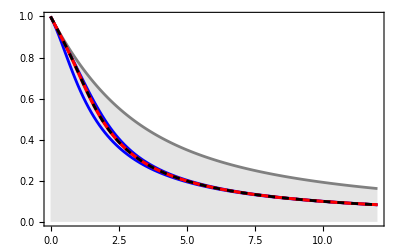

```mathematica
(*Λ=2;*)N0=2;
w[i_,j_,k_]:=-2/N0^2canonize@ w[i+j+k,0]+1/N0 canonize@w[i,j+k]+1/N0 canonize@w[j,i+k]+1/N0 canonize@w[k,j+i];
w0[i_,j_,k_]:=w@@SortBy[{i,j,k},Abs];
w[0,0]=1;
eqmn[n_,m_]/;n>=0:=Sum[w0[i,n-i,m],{i,0,n-1}]+m /N0^2 canonize@w[m+n,0]+β canonize@w[n+1,m]-β canonize@w[n-1,m]//Expand;
updownpair[λ_,matrix_,eq_]:=Block[{var1=Cases[eq,w[x__],Infinity]//Union,rule,matrixwithrule,varsdp},
rule=Reduce[(eq/.β->1/λ)==0,var1]//ToRules;
matrixwithrule=matrix/.rule//Expand;
varsdp=Cases[matrix,w[__],Infinity]//Union;
w[1,0]/.{ConicOptimization[w[1,0],VectorGreaterEqual[{#,0},{"SemidefiniteCone", Length[#[[1]]]}]&[matrixwithrule],varsdp],ConicOptimization[-w[1,0],VectorGreaterEqual[{#,0},{"SemidefiniteCone", Length[#[[1]]]}]&[matrixwithrule],varsdp]}];
updowncurve[λlist_,Λ_]:=Block[{eq,op,matrix},
(*var=canonize/@(w@@@Flatten[Table[{i,j},{i,-Λ,Λ},{j,-Abs[Λ-Abs[i]],Λ-Abs[i]}],1])//Union;*)
eq=(eqmn@@@(Flatten[Table[{i,j},{i,0,Λ+3},{j,-Abs[Λ+3-Abs[i]],Λ+3-Abs[i]}],1])//Union);
op=Cases[Flatten[Table[{i,j},{i,-Floor[Λ/2],Floor[Λ/2]},{j,-Floor[Λ/2],Floor[Λ/2]}],1],x_/;Norm[x,1]<=Floor[Λ/2]];
matrix=Outer[canonize[w@@(#1+#2)]&,op,-op,1];
updownpair[#,matrix,eq]&/@λlist//Transpose];
λlist=Range[1/10,12,1/10];
l2up=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@updowncurve[λlist,2]),2][[2]];
l4updown=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@updowncurve[λlist,4]),2];
l6updown=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@updowncurve[λlist,6]),2];
analist=Join[{{0,1}},Transpose[{λlist,w1analyticuN[#,2]&/@λlist}],1];
lowplot=ListPlot[l2up,Joined->True(*,PlotMarkers->{cross,0.023}*),Frame->True,PlotStyle->Gray,Filling->Axis,PlotRange->{{0,12},{0,1}},RotateLabel->False,FrameStyle->Thick];
Λ4pl=ListPlot[l4updown,Joined->True,PlotStyle->{Blue,Blue}];
Λ6pl=ListPlot[l6updown,Joined->True,PlotStyle->{Red,Red}];
anapl=ListPlot[analist,Joined->True,PlotStyle->{Dashed,Black}];
u2pl=Show[lowplot,Λ4pl,Λ6pl,anapl]
```

## SU(2)

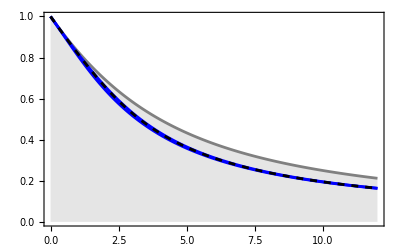

```mathematica
(*Λ=2;*)N0=2;
w[i_,j_]:=1/N0 canonize@w[i+j]+1/N0 canonize@w[i-j];
w0[i_,j_]:=w@@SortBy[{i,j},Abs];
w[0]=1;
eqmn[n_]/;n>=0:=Sum[w0[i,n-i],{i,0,n-1}]+β canonize@w[n+1]-β canonize@w[n-1]-1/N0^2 (n canonize@w[n]+β N0^2(w0[n,1]-w0[n,-1]))//Expand;
updownpair[λ_,matrix_,eq_]:=Block[{var1=Cases[eq,w[x__],Infinity]//Union,rule,matrixwithrule,varsdp},
rule=Reduce[(eq/.β->1/λ)==0,var1]//ToRules;
matrixwithrule=matrix/.rule//Expand;
varsdp=Cases[matrix,w[__],Infinity]//Union;
w[1,0]/.{ConicOptimization[w[1,0],VectorGreaterEqual[{#,0},{"SemidefiniteCone", Length[#[[1]]]}]&[matrixwithrule],varsdp],ConicOptimization[-w[1,0],VectorGreaterEqual[{#,0},{"SemidefiniteCone", Length[#[[1]]]}]&[matrixwithrule],varsdp]}];
updowncurve[λlist_,Λ_]:=Block[{eq,op,matrix},
(*var=canonize/@(w@@@Flatten[Table[{i,j},{i,-Λ,Λ},{j,-Abs[Λ-Abs[i]],Λ-Abs[i]}],1])//Union;*)
op=Cases[Flatten[Table[{i},{i,-Floor[Λ/2],Floor[Λ/2]}],1],x_/;Norm[x,1]<=Floor[Λ/2]];
matrix=Outer[canonize[w@(#1+#2)]&,op,-op,1];
(*op=Cases[Flatten[Table[{i,j},{i,-Floor[Λ/2],Floor[Λ/2]},{j,-Floor[Λ/2],Floor[Λ/2]}],1],x_/;Norm[x,1]<=Floor[Λ/2]];
matrix=Outer[w@@(#1+#2)&,op,-op,1];*)
eq=(eqmn@@@(Table[{j},{j,0,Λ+3}])//Union);
updownpair[#,matrix,eq]&/@λlist//Transpose];
λlist=Range[1/10,12,1/10];
l2up=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@updowncurve[λlist,2]),2][[2]];
l4updown=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@updowncurve[λlist,4]),2];
l6updown=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@updowncurve[λlist,6]),2];
analist=Join[{{0,1}},Transpose[{λlist,w1analytic[#,N0]&/@λlist}],1];
lowplot=ListPlot[l2up,Joined->True(*,PlotMarkers->{cross,0.023}*),Frame->True,PlotStyle->Gray,Filling->Axis,PlotRange->{{0,12},{0,1}},RotateLabel->False,FrameStyle->Thick];
Λ4pl=ListPlot[l4updown,Joined->True,PlotStyle->{Blue,Blue}];
Λ6pl=ListPlot[l6updown,Joined->True,PlotStyle->{Red,Red}];
anapl=ListPlot[analist,Joined->True,PlotStyle->{Dashed,Black}];
su2pl=Show[lowplot,Λ4pl(*,Λ6pl*),anapl]
```

## U(∞)

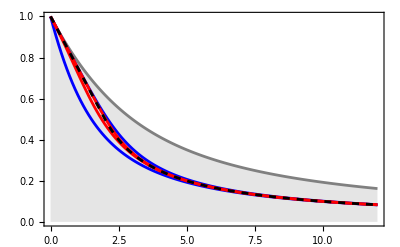

```mathematica
bootuplow[λ_,Λ_]:=Module[{w,matrix,op},
w[k_]:=w[k]=Together[w[k-2]-λ*Sum[w[l]*w[k-l-1],{l,0,k-2}]];
w[0]=1;w[1]=w1;
op=Cases[Flatten[Table[{i},{i,-Floor[Λ/2],Floor[Λ/2]}],1],x_/;Norm[x,1]<=Floor[Λ/2]];
matrix=Outer[canonize[w@Abs@(#1+#2)]&,op,-op,1];
matrix=Table[w[Abs[i-j]],{i,0,Λ},{j,0,Λ}];
(List@@(Reduce@VectorGreaterEqual[{matrix,0},{"SemidefiniteCone", Length@matrix}]//Reduce//N))[[{1,5}]]]
λlist=Range[1/10,12,1/10];
l2up=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@(bootuplow[#,2]&/@λlist//Transpose)),2][[2]];
l4updown=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@(bootuplow[#,4]&/@λlist//Transpose)),2];
l6updown=Join[{{{0,1}},{{0,1}}},({Transpose[{λlist,#1}],Transpose[{λlist,#2}]}&@@(bootuplow[#,6]&/@λlist//Transpose)),2];
analist=Join[{{0,1}},Transpose[{λlist,w1analyticthooft[#]&/@λlist}],1];
lowplot=ListPlot[l2up,Joined->True(*,PlotMarkers->{cross,0.023}*),Frame->True,PlotStyle->Gray,Filling->Axis,PlotRange->{{0,12},{0,1}},RotateLabel->False,FrameStyle->Thick];
Λ4pl=ListPlot[l4updown,Joined->True,PlotStyle->{Blue,Blue}];
Λ6pl=ListPlot[l6updown,Joined->True,PlotStyle->{Red,Red}];
anapl=ListPlot[analist,Joined->True,PlotStyle->{Dashed,Black}];
thooftpl=Show[lowplot,Λ4pl,Λ6pl,anapl]
```